```mathematica
NotebookEvaluate[NotebookDirectory[]<>"FEM_tools_coh.nb"];
```

History Length has been set to 0

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"MeshRefinement_tools.nb"];
```

ElementBoundaryOfSetDistanceFunction completed!

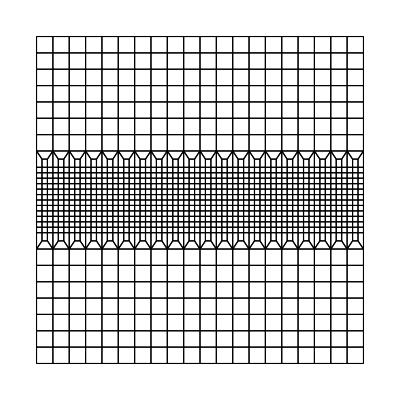

{0.0348758,Null}

30 are to be removed.

{0.0002235,Null}

```mathematica
L=1;H=1;dx=L/20.;udim=2;ndim=2;
(*rg=MyRegionDifference[Rectangle[{0,0},{L,L}],ImplicitRegion[(x-L/2)^2+(y-L/2)^2< L^2/64,{x,y}]];
rg=ImplicitRegion[0≤x≤L&& 0≤y≤L,{x,y}];*)
rg=Rectangle[{0,0},{L,H}];
{m1,coord,ele,eleB,eleP}=Region2Mesh[rg,dx^2,1,0];
(*{m1,coord,ele,eleB,eleP}=Region2MeshHoleList[rg,{{L/2,0}-0.45dx},{{L/2,0.2 H}+0.51dx},dx^2,1,0];*)
distFun1[x_,y_]:=And0[y-0.4,0.6-y];
distFun2[x_,y_]:=And0[y-0.47,0.53-y];
distFun3[x_,y_]:=And0[y-0.49,0.51-y];
{coord,ele}=ElementQ1H1RefinementDist[coord,ele,distFun1,-dx,dx,True];//AbsoluteTiming
dx/=3;
(*{coord,ele}=ElementQ1H1RefinementDist[coord,ele,distFun2,-dx,dx,True];//AbsoluteTiming
dx/=3;*)
(*{coord,ele}=ElementQ1H1RefinementDist[coord,ele,distFun3,-dx,dx,True];//AbsoluteTiming
dx/=3;*)
hole3fun[x_,y_]:=(0.5L-0.8 dx<=y <= 0.5L+0.3dx && x<=0.5)
(*hole3fun[x_,y_]:=(y-0.4)-4(x-0.5L)<=0. &&(y-0.4)+4(x-0.5L)<=0.*)
{ele,coord}=RemoveElementByFunctions[ele,coord,hole3fun];
m1=Abaqus2Mesh[coord,ele];
{coord,ele,eleB,eleP}=Mesh2pureList[m1];//AbsoluteTiming
```

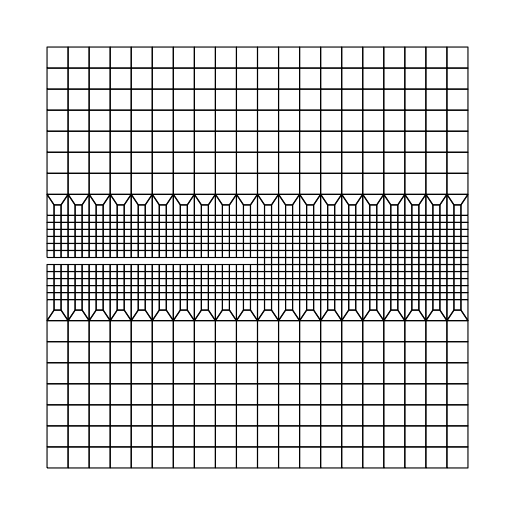

```mathematica
ShowMesh[m1]
```

```mathematica
faceLeft={{0,0}-0.05 dx,{L,0}+0.01 dx};
fixList=FindPoints[coord,faceLeft[[1]],faceLeft[[2]]];
pDirichlet=10.^8;
fixFun[xyz_List]:=ConstantArray[0,ndim];
fixValues=BCValuesFunc[fixList,coord,fixFun,ndim];
dofFix=DofIndexValue[fixList,fixValues];

faceList=FindPoints[coord,{0,L}-0.01dx,{L,L}+0.001dx];
fixU=faceList;
fixFun2[xyz_List]:={0.,-10.^-3};
fixFun2[xyz_List]:=10.^-3{0,1};
fixValues2=BCValuesFunc[faceList,coord,fixFun2,ndim];
dofFix2=DofIndexValue[faceList,fixValues2];
dofFix=Join[dofFix,dofFix2,2];
```

```mathematica
ndim=2;gpr=(*Q9ic3m;*)Q4ic2m;endn=ElementShapeNdN["Q1"(*"Q2S"*),gpr];endnN=endn[[All,1]];endndN=endn[[All,2;;]];
weighL=gpr[[All,-1]];

gprB=L2ic21m;
endnB=ElementShapeNdN["L1",gprB];endnNB=endnB[[All,1]];endndNB=endnB[[All,2;;]];
weighLB=gprB[[All,-1]];
```

```mathematica
{Rindex,Kindex}=RKindexFEM[ele,2];
```

```mathematica
lc0=0.7dx;morder0=1;mat0={(*25.85 10^9, 0.18,*)210,0.3, 0,2.7 10^-3 (*1000000*),lc0,0,morder0};
islinear=True;dt=1;dt0=0.02;dtMin= 10^-4;nnode=Length[coord];ndof=nnode ndim;
uvw=ConstantArray[0.,{nnode,ndim}];pMid={1};fPMid={};ctime=0.;eH={};
(*ResiBC=ResidualOfElementSet[weighLB,endnNB,endndNB,coord,forceEle,{10.^4,0}];*)
printInterval=20;freeInterval=60000;nonlinearStep=If[islinear,1,10];incHistory={};
Hdirect=Table[0.,{Length[ele]},{Length[weighL]}];
HdirectN1=Hdirect;
HdirectN2=Hdirect;
nGP=Length[weighL];
tTotle=100;
forceList={};
tforceList=0.;
normIncL={};
```

```mathematica
AbortOnMessage[]
```

$Aborted

Finish all step

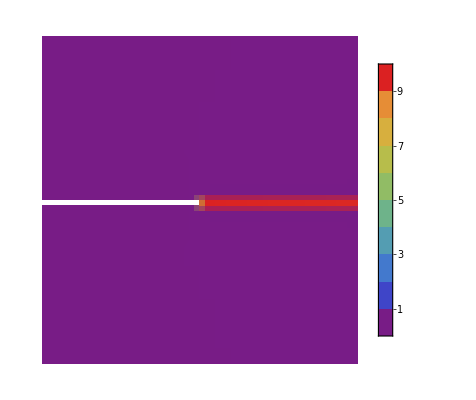

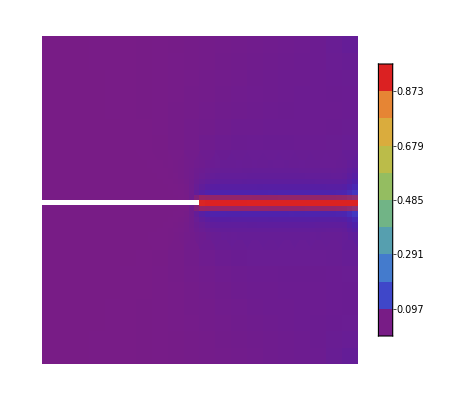

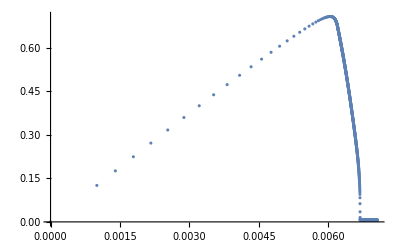

```mathematica
AbortReady[];
Do[
Label[dtHalf];
(*If[uvw[[faceList[[1]]]][[1]]>0.0005,dt=0.2 10^-3];*)
(*{clist,vlist}=AlphaMethod[duvw,uvw,dt];*)
(*nonvarList=NOMCombineVarsToArray[N[gm0],N[Df0],N[clist],N[vlist]];*)
(*HdirectMax=TwoTableMaxEach[HdirectMax,Hdirect[[All,All,1]]];
(*{Rp,Kp}=FemAllMatrixPFs[ls,weighL,endnN,endndN,coord,ele,HdirectMax];*)
{Rp,Kp}=FemAllMatrixPFsPara[ls,weighL,endnN,endndN,coord,ele,HdirectMax,RindexPf,KindexPf];
DirichletApply[Kp,Rp,pfdofFix,pDirichlet];
pfList=LinearSolve[Kp,Rp];*)
ctime+=dt;
uvwN=uvw;incT=ConstantArray[0.,ndof];
AppendTo[eH,{uvwN[[fixU[[1]]]][[2]],Max[Hdirect]/( mat0[[4]]/mat0[[5]])}];
normIncL={};
Do[
(*{Rsp,Ksp,Hdirect}=FemAllMatrixPFuvwPara[weighL,endnN,endndN,coord,uvwN,pfList,ele,Di,GcL,MohrCoumbC,Rindex,Kindex,OneElementMatrixPFuvwPara2D];*)
(*{Rsp,Ksp,Hdirect,fixElementList0,fixDirectionList0}=FemAllMatrixVD2d[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrixVD2d];*)
(*{Rsp,Ksp,Hdirect,fixElementList0,fixDirectionList0}=FemAllMatrixVD2dMix[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrix2Delastic,OneElementMatrixVD2d,OneElementMatrixFix2d,fixElementList0,fixDirectionList0,damagePara0];(*worked*)
*)
{Rsp,Ksp,Hdirect}=FemAllMatrixVD2d[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrixVD2d];
(*AppendTo[KList,Rsp];*)
(*FemAllMatrixPFuvw[weighL,endnN,endndN,coord,uvwN,pfList,ele,Di,GcL,MohrCoumbC,MaximalEnergyDirection2D,WeakPlane2D];*)
(*Hdirect[[All,All,1]]*=ls;*)
Rsp*=-1.;
tforceList=Join[uvwN[[fixU[[1]]]],-{Total[ExtractNodeForce[Rsp,fixU,ndim,1]],Total[ExtractNodeForce[Rsp,fixU,ndim,2]]}];
(*Rsp+=ctime ResiBC;*)
NLDirichletApplySymF[ndim,uvwN,Ksp,Rsp,dofFix,ctime];
uv=LinearSolve[Ksp,Rsp,Method->"Pardiso"];
incT+=uv;
uvwN+=Vector2Matrix[uv,udim];
normInc=Norm[uv]/(Norm[incT]+10.^-20);
If[!NumericQ[normInc],Print["Error, symbol in nomrInc;"];Abort[]];
AppendTo[normIncL,normInc];
(*Print[normInc,"it",j];*)If[Norm[uv]/(Norm[incT]+10.^-20)≤1. 10^-6,Break[]];kIti=j;If[(j==nonlinearStep || Total[normIncL]>5)&& (!islinear),Print["Warning, divergent at ctime=",ctime, " with dt=",dt];incHistory[[-1]]=100;
ctime-=dt;
dt=dt/2;
If[dt<dtMin,Print["Error, minimal time increment reached!"];Abort[]];
Goto[dtHalf]];,{j,nonlinearStep}];
If[ctime≥tTotle,Break[]];
Print["step:",i," time:",ctime];
uvw=uvwN;
dt=dt0 Max[ 20/(1+Max[Hdirect]/( mat0[[4]]/mat0[[5]]))^2, 50 10^-3];
AppendTo[forceList,tforceList];
AppendTo[incHistory,kIti];
If[kIti>15,dt=dt/2.];
If[Length[incHistory]>3 && Total[incHistory[[-3;;-1]]]<22 && !islinear,dt*=2.];
If[Mod[i-1,printInterval]==0,(*SaveToCell[uvw,"uvw"<>ToString[ctime]];*)Print[Plot2DField0[uvwN[[All,1]],m1]];Print[Plot2DField0[uvwN[[All,2]],m1]];Print[Plot2DField0[#/(#+mat0[[4]]/mat0[[5]]),m1]&[MeanGaussPointToNode[Hdirect,ele,coord]]];(*Print[Plot2DField[pfList,m1]]*)];
AppendTo[fPMid,uvw[[pMid]]];AbortCheck[];
(*AppendTo[resP1,Flatten[uvw[[p1]]]];*)
(*Print[Plot2DField[ acc[[All,2]],m1]];*)
(*Print[Contour2DField[ uvw[[All,1]],m1],Contour2DField[ vel[[All,1]],m1],Contour2DField[ acc[[All,1]],m1]];*)
(*Print[Contour2DField[NormList[ uvw],m1],Contour2DField[ NormList[acc],m1],Contour2DField[ NormList[vel],m1]];*)
(*Print[Contour2DField[ uvw[[All,1]],m1],Contour2DField[ uvw[[All,2]],m1],Contour2DField[ acc[[All,1]],m1]];
Print[Contour2DField[ acc[[All,2]],m1],Contour2DField[ vel[[All,1]],m1],Contour2DField[ vel[[All,2]],m1]]*)
,{i,1000}];
Print["Finish all step"];
(*HnodeValue=GaussPointToNode[Hdirect,ele,coord,endnN];*)
HnodeValue=MeanGaussPointToNode[Hdirect,ele,coord];
Plot2DField0[HnodeValue,m1]
Plot2DField0[HnodeValue/(HnodeValue+mat0[[4]]/mat0[[5]]),m1]
ListPlot[forceList[[All,{2,4}]],PlotRange->All]
SaveToCell[forceList,"Node lc:"<>ToString[Length[coord]]<>" and "<>ToString[N[lc0]]<>"fmax:"<>ToString[InputForm[Round1[forceList[[Ordering[forceList[[All,2]],-1]]],5]]]]
{ListPlot[forceList[[All,{1,3}]]],ListPlot[forceList[[All,{1,4}]]],ListPlot[forceList[[All,{2,3}]]],ListPlot[forceList[[All,{2,4}]]]}
```